```mathematica
{{1,3},{2,5},{3,4},{4,3},{5,2},{5,1}}-{1,4}
```

Thread::tdlen: Objects of unequal length in {{1,3},{2,5},{3,4},{4,3},{5,2},{5,1}}+{-1,-4} cannot be combined.

{-1,-4}+{{1,3},{2,5},{3,4},{4,3},{5,2},{5,1}}

## Prob 1.1-2

```mathematica
X={{1,3},{2,5},{3,4},{4,3},{5,2},{5,1}};
Xcent=#-Mean[X]&/@X
```

{{-7/3,0},{-4/3,2},{-1/3,1},{2/3,0},{5/3,-1},{5/3,-2}}

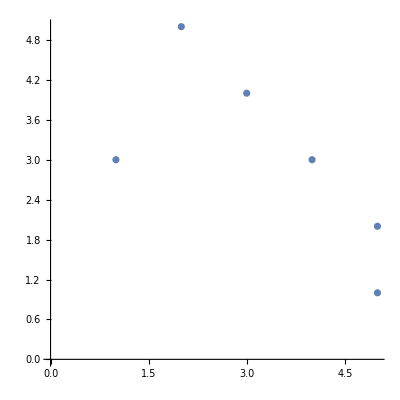

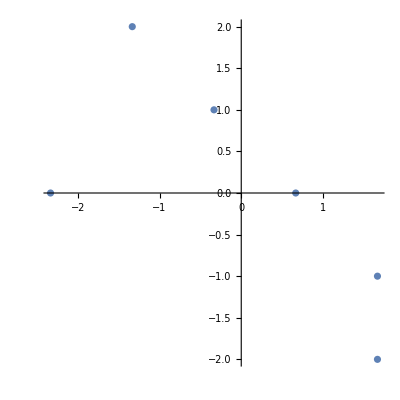

```mathematica
ListPlot[X,PlotRange->{{0,Automatic},{0,Automatic}},AspectRatio->1]
ListPlot[Xcent,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}},AspectRatio->1,AxesOrigin->{0,0}]
```

```mathematica
{u,s,v}=N@SingularValueDecomposition[Transpose[Xcent].Xcent]
```

{{{-0.775872,0.630891},{0.630891,0.775872}},{{19.8384,0.},{0.,3.4949}},{{-0.775872,0.630891},{0.630891,0.775872}}}

```mathematica
{{0.7589654749242356,-0.6511308684688735},{0.6511308684688735,0.7589654749242357}}.{{124.61178575186362,0.},{0.,19.388214248136375}}.Transpose[{{0.7589654749242356,-0.6511308684688736},{0.6511308684688735,0.7589654749242357}}]
```

{{80.,52.},{52.,64.}}

```mathematica
Transpose[X].X
```

{{80,52},{52,64}}

```mathematica
u//MatrixForm
```

(-0.775872 | 0.630891
0.630891 | 0.775872)

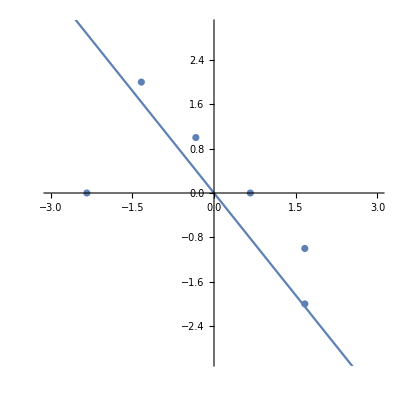

```mathematica
Show[Plot[u[[1,1]]/u[[2,1]]x,{x,-5,5}],ListPlot[Xcent],PlotRange->{{-3,3},{-3,3}},AspectRatio->1]
```

## Prob 1.3

```mathematica
X1=Xcent[[1;;4]]
X2=Xcent[[5;;6]]
```

{{-7/3,0},{-4/3,2},{-1/3,1},{2/3,0}}

{{5/3,-1},{5/3,-2}}

```mathematica
Transpose[{{1,2}}]
```

{{1},{2}}

```mathematica
{{1},{2}}.{{1,2}}
```

{{1,2},{2,4}}

```mathematica
(#-m1)&/@X1
Plus@@((#-m1).Transpose[{#-m1}]&/@X1)+Plus@@((#-m2).Transpose[{#-m2}]&/@X2)
```

{{-3/2,-3/4},{-1/2,5/4},{1/2,1/4},{3/2,-3/4}}

{33/4}

```mathematica
m1=Mean[X1];m2=Mean[X2];
Sw=Plus@@((#-m1).Transpose[{#-m1}]&/@X1)+Plus@@((#-m2).Transpose[{#-m2}]&/@X2);
w=1/N@@Sw*(m1-m2)
```

{-0.30303,0.272727}

{-0.30303,0.272727}

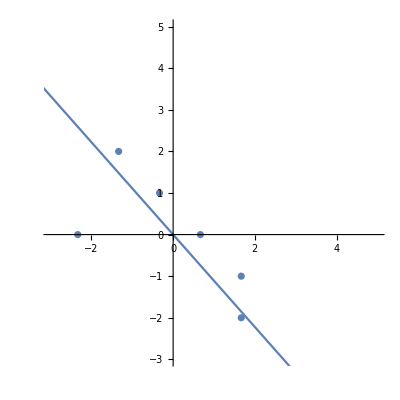

```mathematica
m1=Mean[X1];m2=Mean[X2];
Sw=Plus@@((#-m1).Transpose[{#-m1}]&/@X1)+Plus@@((#-m2).Transpose[{#-m2}]&/@X2);
w=1/N@@Sw*(m1-m2)
Show[Plot[w[[1]]/w[[2]]x,{x,-5,5}],ListPlot[Xcent],PlotRange->{{-3,5},{-3,5}},AspectRatio->1]
```

```mathematica
(#-m1).Transpose[#-m1]&/@X1
(#-m1)^2&/@X1
```

{45/16,29/16,5/16,45/16}

{{9/4,9/16},{1/4,25/16},{1/4,1/16},{9/4,9/16}}

## Prob2 - k-NN

```mathematica
C1={{1,1},{2,2},{2,3}};C2={{3,2},{3,3},{4,4}};
```

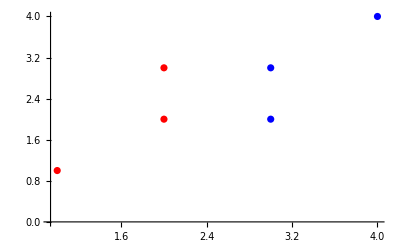

```mathematica
ListPlot[{C1,C2},PlotStyle->{Red,Blue}]
```

```mathematica
test=Flatten[Table[{i,j},{i,Range[0,5,0.01]},{j,Range[0,5,0.01]}],1]
ListPlot[test]
```

{{0.,0.},{0.,0.01},{0.,0.02},{0.,0.03},{0.,0.04},{0.,0.05},{0.,0.06},{0.,0.07},{0.,0.08},{0.,0.09},{0.,0.1},{0.,0.11},{0.,0.12},{0.,0.13},{0.,0.14},{0.,0.15},250969,{5.,4.85},{5.,4.86},{5.,4.87},{5.,4.88},{5.,4.89},{5.,4.9},{5.,4.91},{5.,4.92},{5.,4.93},{5.,4.94},{5.,4.95},{5.,4.96},{5.,4.97},{5.,4.98},{5.,4.99},{5.,5.}}
 |  |  |  |

-Graphics-

```mathematica
Nearest[crit,{2.5,2.5}]
```

{1,1,2,2}

```mathematica
nearest=Nearest[Join[C1,C2]]/@test;
Select
```

{{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},{{1,1}},250951,{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}},{{4,4}}}
 |  |  |  |

```mathematica
assocClass=AssociationMap[If[MemberQ[C1,#],1,If[MemberQ[C2,#],2]]&,Join[C1,C2]];
```

```mathematica
assocClass
```

<|{1,1}→1,{2,2}→1,{2,3}→1,{3,2}→2,{3,3}→2,{4,4}→2|>

```mathematica
If[MemberQ[C1][#],1,If[MemberQ[C2][#],2]]&/@Join[C1,C2]
```

{Null,Null,Null,Null,Null,Null}

```mathematica
crit=Join[#->1&/@C1,#->2&/@C2];
nearest=Nearest[crit,#]&/@test;
clustering=AssociationThread[test,nearest]
```

<|{0.,0.}→{1},{0.,0.01}→{1},{0.,0.02}→{1},{0.,0.03}→{1},{0.,0.04}→{1},{0.,0.05}→{1},{0.,0.06}→{1},{0.,0.07}→{1},{0.,0.08}→{1},{0.,0.09}→{1},{0.,0.1}→{1},{0.,0.11}→{1},250977,{5.,4.89}→{2},{5.,4.9}→{2},{5.,4.91}→{2},{5.,4.92}→{2},{5.,4.93}→{2},{5.,4.94}→{2},{5.,4.95}→{2},{5.,4.96}→{2},{5.,4.97}→{2},{5.,4.98}→{2},{5.,4.99}→{2},{5.,5.}→{2}|>
 |  |  |  |

```mathematica
clustering[{0.,0.}]
```

{1}

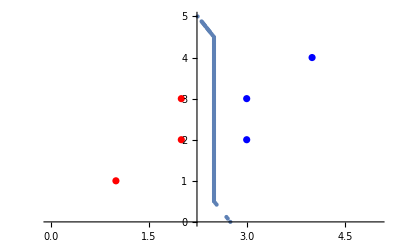

```mathematica
boundary=Select[test,Length[Union[clustering[#]]]>1&];
Show[ListPlot[boundary],ListPlot[{C1,C2},PlotStyle->{Red,Blue}],PlotRange->{{0,5},{0,5}}]
```

{{0.,-3.},{0.,-2.95},{0.,-2.9},{0.,-2.85},{0.,-2.8},{0.,-2.75},{0.,-2.7},{0.,-2.65},{0.,-2.6},{0.,-2.55},{0.,-2.5},{0.,-2.45},{0.,-2.4},10226,{5.,6.45},{5.,6.5},{5.,6.55},{5.,6.6},{5.,6.65},{5.,6.7},{5.,6.75},{5.,6.8},{5.,6.85},{5.,6.9},{5.,6.95},{5.,7.}}
 |  |  |  |

<|{0.,-3.}→{1},{0.,-2.95}→{1},{0.,-2.9}→{1},{0.,-2.85}→{1},{0.,-2.8}→{1},{0.,-2.75}→{1},{0.,-2.7}→{1},{0.,-2.65}→{1},{0.,-2.6}→{1},10233,{5.,6.6}→{2},{5.,6.65}→{2},{5.,6.7}→{2},{5.,6.75}→{2},{5.,6.8}→{2},{5.,6.85}→{2},{5.,6.9}→{2},{5.,6.95}→{2},{5.,7.}→{2}|>
 |  |  |  |

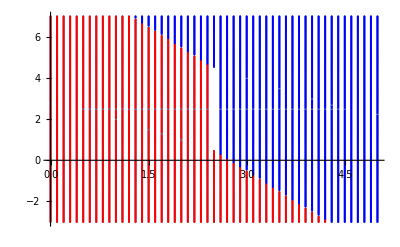

```mathematica
test=Flatten[Table[{i,j},{i,Range[0,5,0.1]},{j,Range[-3,7,0.05]}],1]
crit=Join[#->1&/@C1,#->2&/@C2];
nearest=Nearest[crit,#]&/@test;
clustering=AssociationThread[test,nearest]
filling=Select[test,Length[Union[clustering[#]]]==1&];
ListPlot[ParallelTable[Style[x,If[clustering[x]=={1},Red,If[clustering[x]=={2},Blue]]],{x,filling}]]
```

```mathematica
test=Flatten[Table[{i,j},{i,Range[0,5,0.1]},{j,Range[-3,7,0.05]}],1]
crit=Join[#->1&/@C1,#->2&/@C2];
nearest=Nearest[crit,#]&/@test;
clustering=AssociationThread[test,nearest]
filling=Select[test,Length[Union[clustering[#]]]==1&];
ListPlot[ParallelTable[Style[x,If[clustering[x]=={1},Red,If[clustering[x]=={2},Blue]]],{x,filling}]]
```

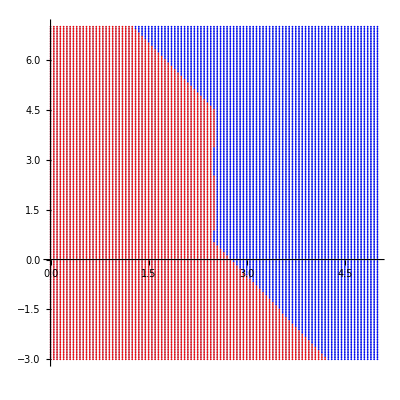

```mathematica
test=Flatten[Table[{i,j},{i,Range[0,5,0.05]},{j,Range[-3,7,0.05]}],1];
classifier=Classify[Join[#->1&/@C1,#->2&/@C2],Method->{"NearestNeighbors","NeighborsNumber"->1}];
clustering=AssociationThread[test,classifier[test]];
ListPlot[ParallelTable[Style[x,If[clustering[x]==1,Red,If[clustering[x]==2,Blue]]],{x,test}],AspectRatio->1]
```

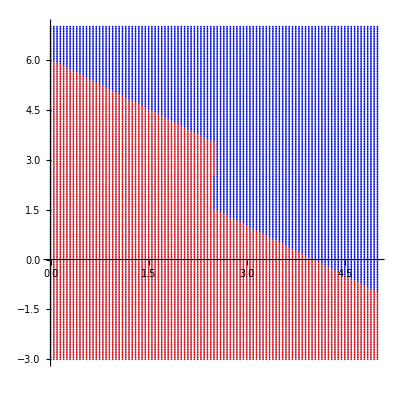

```mathematica
test=Flatten[Table[{i,j},{i,Range[0,5,0.05]},{j,Range[-3,7,0.05]}],1];
classifier=Classify[Join[#->1&/@C1,#->2&/@C2],Method->{"NearestNeighbors","NeighborsNumber"->3}];
clustering=AssociationThread[test,classifier[test]];
ListPlot[ParallelTable[Style[x,If[clustering[x]==1,Red,If[clustering[x]==2,Blue]]],{x,test}],AspectRatio->1]
```

## Misc.

```mathematica
M=RandomReal[{0,10},{3,3}]
{u,s,v}=SingularValueDecomposition[M]
```

{{9.82626,2.37753,3.40661},{9.77615,4.66713,3.29554},{3.28386,4.38878,3.64178}}

{{{-0.638338,0.472946,0.607328},{-0.686168,0.00795717,-0.7274},{-0.348853,-0.881056,0.319441}},{{16.4677,0.,0.},{0.,3.62524,0.},{0.,0.,1.00382}},{{-0.857807,0.505295,-0.0940457},{-0.379599,-0.746207,-0.546882},{-0.346514,-0.433419,0.831911}}}

```mathematica
a={1,2,3}
a.M.a
a.Transpose[M].a
```

{1,2,3}

151.756

151.756

```mathematica
M
```

{{9.82626,2.37753,3.40661},{9.77615,4.66713,3.29554},{3.28386,4.38878,3.64178}}

```mathematica
M==Transpose[M]
```

False

```mathematica
s
```

{{16.4677,0.,0.},{0.,3.62524,0.},{0.,0.,1.00382}}

```mathematica
a={1,2,3}
a.DiagonalMatrix[{1,1,1}].a
```

{1,2,3}

14

```mathematica
Z=RandomReal[{0,10},{2,2}]
X=RandomReal[{0,10},{2,2}]
Y=RandomReal[{0,10},{2,2}]
Sx=(X+Transpose[X])
Sy=(Y+Transpose[Y])
A=Inverse[Sy].Z.Inverse[Sx].Transpose[Z]
B=Inverse[Sx].Transpose[Z].Inverse[Sy].Z
matC=Transpose[Z].Inverse[Sx].Z.Inverse[Sy]
```

{{6.42435,4.3196},{5.80868,2.74581}}

{{1.57434,7.7171},{2.9384,0.865801}}

{{8.5665,6.49251},{5.39022,3.5141}}

{{3.14869,10.6555},{10.6555,1.7316}}

{{17.133,11.8827},{11.8827,7.02821}}

{{0.426258,0.257779},{-0.25553,-0.0965548}}

{{0.172755,0.0718634},{0.033406,0.156948}}

{{-0.0434408,0.543458},{-0.0765131,0.388315}}

```mathematica
SingularValueDecomposition[A][[2]]//MatrixForm
SingularValueDecomposition[B][[2]]//MatrixForm
SingularValueDecomposition[matC][[2]]//MatrixForm
```

(0.566446 | 0.
0. | 0.0436281)

(0.219194 | 0.
0. | 0.112745)

(0.672701 | 0.
0. | 0.0367369)

```mathematica
SingularValueDecomposition[A][[2]]//MatrixForm
SingularValueDecomposition[B][[2]]//MatrixForm
Eigenvalues[A]
Eigenvalues[B]
```

(0.566446 | 0.
0. | 0.0436281)

(0.219194 | 0.
0. | 0.112745)

{0.214482,0.115222}

{0.214482,0.115222}